```mathematica
Block[
{assoc1,assoc2},
assoc1=<|2->3,4->5,6->7,1->9,1.5->7,3.5->9|>;
Print[assoc1[3.5]];
assoc2=<|{3,4}->4,{2,5}->3|>;
Print[assoc2[{2,5}]]
]
```

9

3

```mathematica
Block[
{Ia,Ic,M,n,m,k},
Ia=<||>;Ic=<||>;
M=100;
n=7.41;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
m=RandomInteger[{-M,M}];
k=RandomInteger[{1,2M}];
Print["m = ",m,"; k = ",k,"; Ia = ",Ia[{m,k}]];
Print["k = ",k,"; Ic = ",Ic[k]];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.0130781-6.28408 ⅈ and 0.0358779 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -0.000343791+0.0000196783 ⅈ and 0.0405798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.249224+0.217086 ⅈ and 0.0628184 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00262677-0.00161123 ⅈ and 0.0255809 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.00272991-0.00294913 ⅈ and 0.0327034 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -2.96079×10^-6-0.00151745 ⅈ and 0.0449188 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{ϕ[0]→-1065.61-2437.62 ⅈ,ϕ[1]→-2.61283×10^16-3.04004 ⅈ,A[-2]→195740.+149950. ⅈ,A[-1]→6854.78-14949.5 ⅈ,A[1]→1922.96-3644.96 ⅈ,A[2]→-143.671+95.215 ⅈ,B[-2]→-115.401-44.7502 ⅈ,B[-1]→-885.118-903.157 ⅈ,B[1]→-70472.1+82489.1 ⅈ,B[2]→159093.-43943.8 ⅈ}}

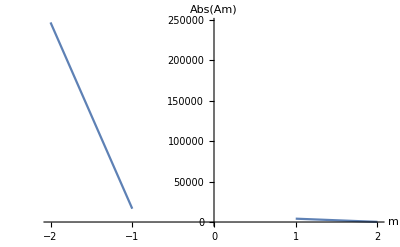

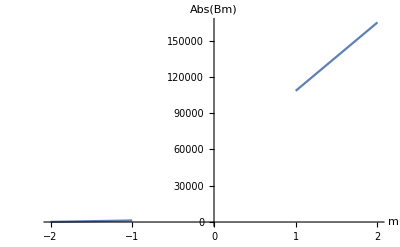

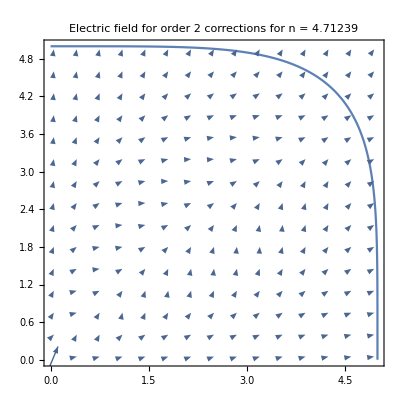

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=2;(* Half the number of coefficients Am or Bm *)
n=N[3π/2];(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=Solve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Am)"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Bm)"}]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -1.75351×10^-6-0.00139468 ⅈ and 0.0460407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 5.8114×10^-6-0.00295147 ⅈ and 0.0458156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -0.0000147523-0.000752579 ⅈ and 0.0471554 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{ϕ[0]→-9904.8-13053.7 ⅈ,ϕ[1]→-2.61283×10^16-14.7082 ⅈ,A[-3]→3.65421×10^6-170968. ⅈ,A[-2]→-260372.-367584. ⅈ,A[-1]→49508.8+119270. ⅈ,A[1]→-6174.35-1269.18 ⅈ,A[2]→182.304+256.954 ⅈ,A[3]→-6.928+25.2385 ⅈ,B[-3]→-165.791-5.61681 ⅈ,B[-2]→1568.43+228.432 ⅈ,B[-1]→-853.679+811.571 ⅈ,B[1]→109425.+39032.1 ⅈ,B[2]→755597.-194090. ⅈ,B[3]→-1.98156×10^6-623121. ⅈ}}

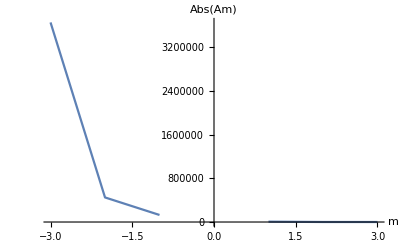

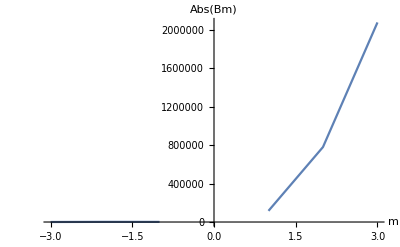

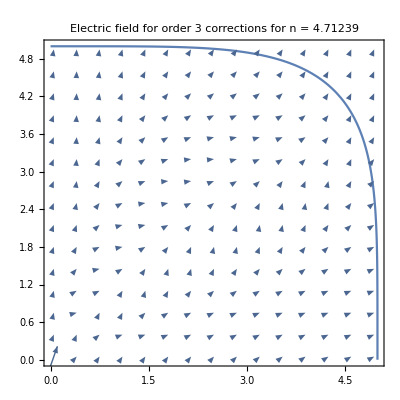

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=3;(* Half the number of coefficients Am or Bm *)
n=N[3π/2];(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=Solve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Am)"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Bm)"}]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -6.65727×10^-6-0.00129348 ⅈ and 0.0317231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.0000178121-0.00245071 ⅈ and 0.062625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.0022709+0.0000203335 ⅈ and 0.0200689 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{ϕ[0]→17542.4+4121.61 ⅈ,ϕ[1]→-2.61283×10^16+6.22858 ⅈ,A[-4]→-2.68863×10^6+2.92906×10^6 ⅈ,A[-3]→-1.09041×10^6+356838. ⅈ,A[-2]→-71836.8+413042. ⅈ,A[-1]→109127.-116156. ⅈ,A[1]→8077.86+4677.38 ⅈ,A[2]→-1644.58-52.106 ⅈ,A[3]→146.722+68.374 ⅈ,A[4]→-13.0702-1.83876 ⅈ,B[-4]→-5.37361+14.544 ⅈ,B[-3]→100.855-85.2967 ⅈ,B[-2]→-459.482+108.405 ⅈ,B[-1]→-5606.68-238.202 ⅈ,B[1]→-260700.+31440.9 ⅈ,B[2]→179514.-346842. ⅈ,B[3]→728918.+522496. ⅈ,B[4]→1.48883×10^6+2.47735×10^6 ⅈ}}

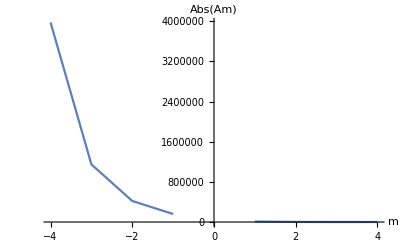

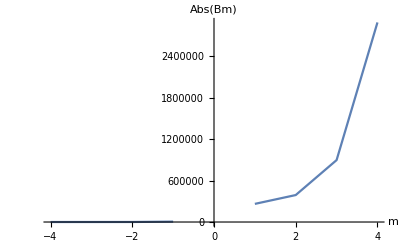

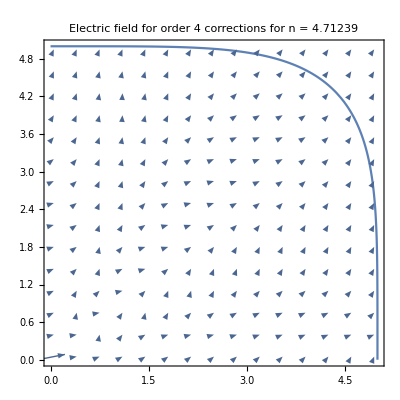

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=4;(* Half the number of coefficients Am or Bm *)
n=N[3π/2];(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=Solve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Am)"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Bm)"}]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.000255864-0.0000266529 ⅈ and 0.0504987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.0000363778-0.00144748 ⅈ and 0.0805126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -0.0000350056+0.000663621 ⅈ and 0.0548344 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {«1»} may contain significant numerical errors.

{{ϕ[0]→-2023.71+14214.1 ⅈ,ϕ[1]→-2.61283×10^16-6.96708 ⅈ,A[-5]→-6.84223×10^6-1.2071×10^7 ⅈ,A[-4]→-4.76543×10^6-8.27211×10^6 ⅈ,A[-3]→-86620.2-688114. ⅈ,A[-2]→5866.16-113178. ⅈ,A[-1]→32552.9+83202.5 ⅈ,A[1]→-3956.37+443.922 ⅈ,A[2]→458.03+149.7 ⅈ,A[3]→-74.4331-17.9021 ⅈ,A[4]→12.7645+0.269413 ⅈ,A[5]→-0.453982+0.0728606 ⅈ,B[-5]→0.662605-1.3603 ⅈ,B[-4]→-11.117+10.7326 ⅈ,B[-3]→30.452+47.0489 ⅈ,B[-2]→-623.869-158.455 ⅈ,B[-1]→2372.02-2365.92 ⅈ,B[1]→15824.-48496.5 ⅈ,B[2]→-172006.-100764. ⅈ,B[3]→-262347.+770138. ⅈ,B[4]→-748436.-5.27487×10^6 ⅈ,B[5]→8.48464×10^6+6.59393×10^6 ⅈ}}

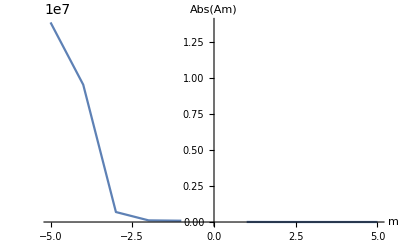

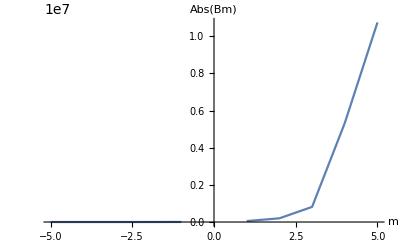

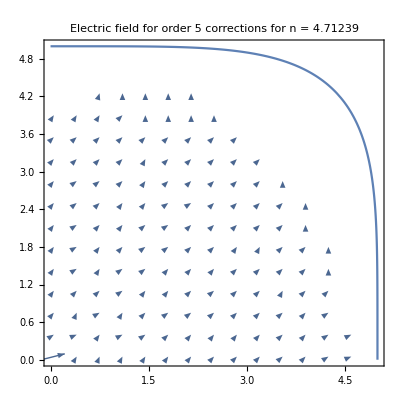

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=5;(* Half the number of coefficients Am or Bm *)
n=N[3π/2];(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=Solve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Am)"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B[m]/.soln,1]]},{m,-M,M}],PlotRange->All,AxesLabel->{"m","Abs(Bm)"}]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```